```mathematica
Needs["MaTeX`"]
MaTeX["x^2"]

SetOptions[
MaTeX,
"Preamble"->{
"\\usepackage{color,txfonts}",
"\\definecolor{dkgreen}{rgb}{0,0.6,0}",
"\\definecolor{orange}{rgb}{1,0.55,0}",
"\\definecolor{lightblue}{rgb}{0.68,0.85,0.9}",
"\\definecolor{darkblue}{rgb}{0,0,1}"
}
];
MaTeX["\\color{red}\\sqrt{x}"]
MaTeX["\\color{dkgreen}\\sqrt{x}"]
MaTeX["\\color{orange}\\sqrt{x}"]
MaTeX["\\color{lightblue}\\sqrt{x}"]
MaTeX["\\color{darkblue}\\sqrt{x}"]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

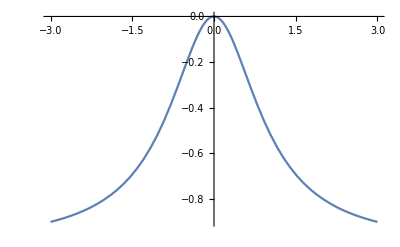

```mathematica
Plot[-x^2/(1+x^2),{x,-3,+3}]
```

```mathematica
VF[{θ_,dh_},d_]:={-Sin[θ]+Sin[θ](d-dh),Sin[θ]^2}
V[{θ_,dh_},d_]:=1-Cos[θ]+1/2(d-dh)^2
D[V[{θ,dh},d],{{θ,dh}}].VF[{θ,dh},d]//Simplify
```

-Sin[θ]^2

```mathematica
points =Tuples[{{-π,-π/2,0-0.2,0+0.2,π/2,+π},{-1,0,+1,+2,+3}}];(*points =Tuples[{{-π,-π/2,0-0.2,0+0.2,π/2,+π},{-2,-1,0,+1,+2,+3,+4}}];*)
(*points = Tuples[{-1,0,1},2]*)
```

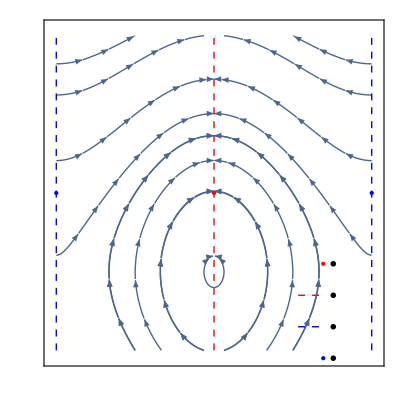

```mathematica
Show[
StreamPlot[
VF[{θ,dh},#1],
{θ,-π,+π},
{dh,#1-#2,#1+#2},
RegionFunction->Function[{θ,dh,θd,dhd,n},((θ-π)/(π/2))^2+(dh-(-2))^2≥ 2],BoundaryStyle->None,
StreamPoints->{points,0.001,6},
(*Epilog->Point[points],*)
Epilog->{
{Red, PointSize[Large],Point[{0,#1}]},
{Blue, PointSize[Large],Point[{-π,#1}]},
{Blue, PointSize[Large],Point[{+π,#1}]},
{Red,Dashed,Line[{{0,#1-#2},{0,#1+#2}}]},
{Blue,Dashed,Line[{{-π,#1-#2},{-π,#1+#2}}]},
{Blue,Dashed,Line[{{+π,#1-#2},{+π,#1+#2}}]},
},
FrameTicks->{
{
{
{-2,MaTeX["-2"]},
{-1,MaTeX["-1"]},
{0,MaTeX["0"]},
{+1,MaTeX["+1"]},
{+2,MaTeX["+2"]},
{+3,MaTeX["+3"]},
{+4,MaTeX["+4"]}
},None
},
{
{
{-π,MaTeX["-\\pi \\vphantom{\\frac{\\pi}{2}}"]},
{-π/2,MaTeX["-\\frac{\\pi}{2}"]},
{0,MaTeX["0 \\vphantom{\\frac{\\pi}{2}}" ]},
{+π/2,MaTeX["+\\frac{\\pi}{2}"]},
{+π,MaTeX["+\\pi \\vphantom{\\frac{\\pi}{2}}"]}
},
None
}
},
FrameLabel->{MaTeX["\\theta"],MaTeX["\\hat{d}"]}
]&[1,2],(*]&[1,3],*)
(**)
Graphics[{
{Red, PointSize[Large],Point[{#1-0.1,+0.6+#2}]},
{Text[MaTeX["\\color{red} = \\mathbb{X}_{\\scriptscriptstyle{+}}^{\\scriptscriptstyle{\\star \\star}}"],{#1+0.1,+0.6+#2},{-1,0}]},
{Red, Dashed,Line[{{#1-0.6,+0.2+#2},{#1-0.1,+0.2+#2}}]},
{Text[MaTeX["\\color{red} = \\mathbb{X}_{\\scriptscriptstyle{+}}^{\\scriptscriptstyle{\\star}}"],{#1+0.1,+0.2+#2},{-1,0}]},
{Blue,Dashed, Line[{{#1-0.6,-0.2+#2},{#1-0.1,-0.2+#2}}]},
{Text[MaTeX["\\color{blue} = \\mathbb{X}_{\\scriptscriptstyle{-}}^{\\scriptscriptstyle{\\star}}"],{#1+0.1,-0.2+#2},{-1,0}]},
{Blue, PointSize[Large],Point[{#1-0.1,-0.6+#2}]},
{Text[MaTeX["\\color{blue} = \\mathbb{X}_{\\scriptscriptstyle{-}}^{\\scriptscriptstyle{\\star \\star}}"],{#1+0.1,-0.6+#2},{-1,0}]}
}
]&[3/4 π-0.08,-0.5](*]&[3/4 π-0.2,-1.7]*)
]
```

```mathematica
Export[NotebookDirectory[]<>"stability_atractivity_of_set_disturbance_removal.pdf",%];
```